```mathematica
FullSimplify[
Normalize[D[{x, 1-x},x]].
Normalize[D[{x, x^a},x]], Element[a|x,Reals]]
```

(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a)))

```mathematica
Manipulate[Plot[(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a))),{x,-8,8}],{a,-8,8}]
```

```mathematica
FullSimplify[
Normalize[D[{x, 1-x},x]].
Normalize[D[{x, x^a},x]], Element[a|x,Reals]]
```

(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a)))

```mathematica
Table[(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a))), {a, 0, 50, .01}]
```

{(0.+x)/(x √(2+0./1^1.)),(1+x)/(x √(2+1)),4997,(x-1)/(x 1),(x-50. x^50.)/(x √(2+5000. 1))}
 |  |  |  |

```mathematica
Plot[
Out[4],{x,0,1}, PlotLegends->"Expressions"]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::munfl: (4.17327×10^-10)^32.81 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.17327×10^-10)^32.82 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.17327×10^-10)^32.83 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Identity::argx: Identity called with 4096 arguments; 1 argument is expected.

General::stop: Further output of Identity::argx will be suppressed during this calculation.

$Aborted

```mathematica
Table[(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a))), {a, 0, 50}]
```

{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))}

```mathematica
1+1
```

2

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

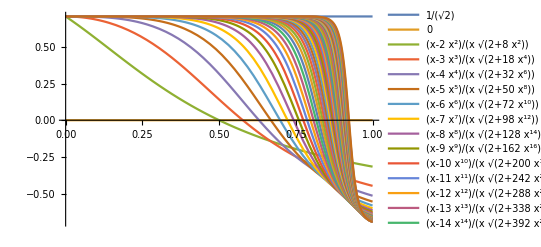

```mathematica
Plot[
{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, 0, 1}, PlotLegends->"Expressions"]
```

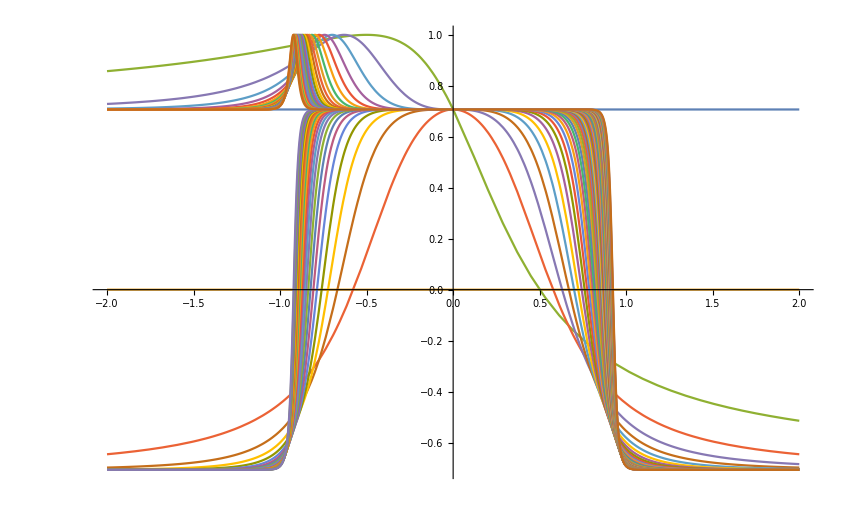

```mathematica
Plot[
{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, -2, 2}]
```

```mathematica
Plot3D[
{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
Param
```

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 π},{u,0,2 π},Mesh->Automatic,MeshStyle->Directive[RGBColor[0.1,0.,0.9400000000000001],Opacity[1.],AbsoluteThickness[2.]]]
```

-Graphics3D-

```mathematica
Show[%14,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Sin[t],u Cos[t],t/3},{t,0,15},{u,-1,1}]
```

-Graphics3D-

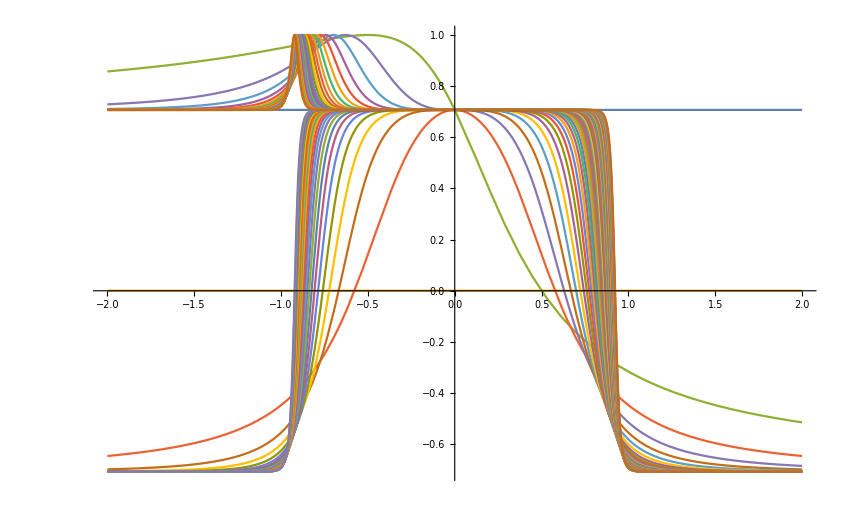

```mathematica
Plot[
{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, -2, 2}]
```

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

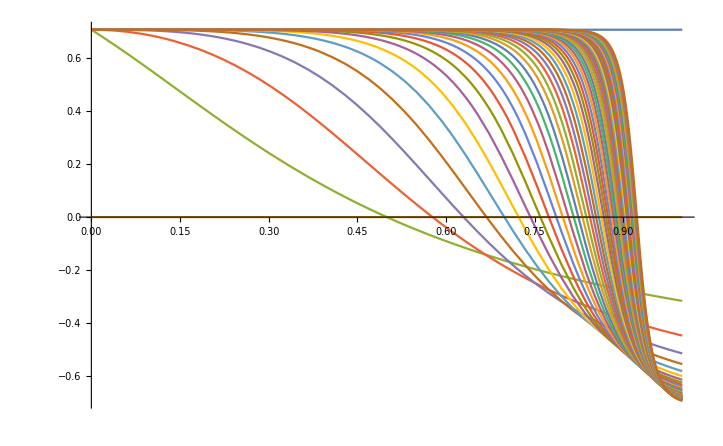

```mathematica
Plot[
{1/(√2),0,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, 0, 1}]
```

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

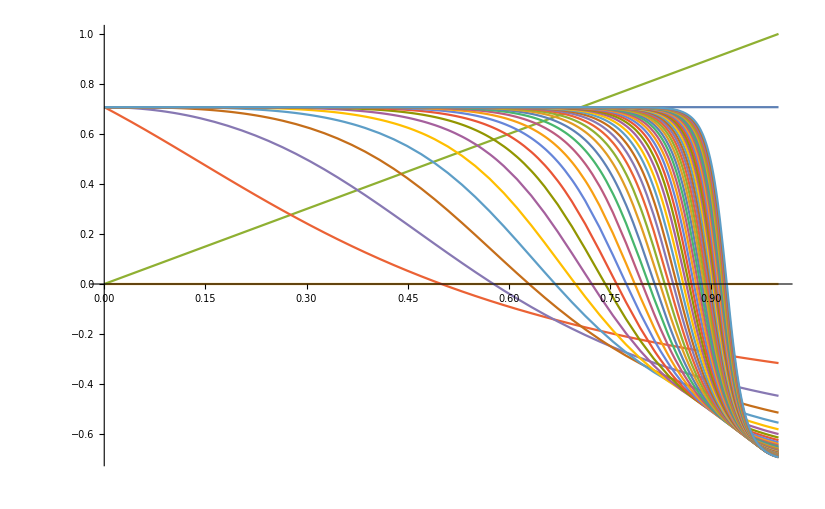

```mathematica
Plot[
{1/(√2),0,x,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, 0, 1}]
```

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

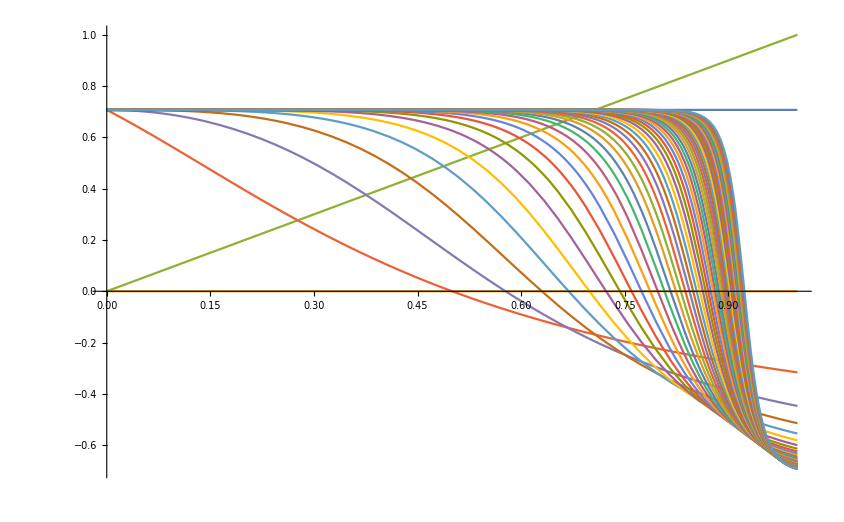

```mathematica
Plot[
{1/(√2),0,x,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, 0, 1}]
```

```mathematica
Plot[
{1/(√2),0,x,(x-2 x^2)/(x √(2+8 x^2)),(x-3 x^3)/(x √(2+18 x^4)),(x-4 x^4)/(x √(2+32 x^6)),(x-5 x^5)/(x √(2+50 x^8)),(x-6 x^6)/(x √(2+72 x^10)),(x-7 x^7)/(x √(2+98 x^12)),(x-8 x^8)/(x √(2+128 x^14)),(x-9 x^9)/(x √(2+162 x^16)),(x-10 x^10)/(x √(2+200 x^18)),(x-11 x^11)/(x √(2+242 x^20)),(x-12 x^12)/(x √(2+288 x^22)),(x-13 x^13)/(x √(2+338 x^24)),(x-14 x^14)/(x √(2+392 x^26)),(x-15 x^15)/(x √(2+450 x^28)),(x-16 x^16)/(x √(2+512 x^30)),(x-17 x^17)/(x √(2+578 x^32)),(x-18 x^18)/(x √(2+648 x^34)),(x-19 x^19)/(x √(2+722 x^36)),(x-20 x^20)/(x √(2+800 x^38)),(x-21 x^21)/(x √(2+882 x^40)),(x-22 x^22)/(x √(2+968 x^42)),(x-23 x^23)/(x √(2+1058 x^44)),(x-24 x^24)/(x √(2+1152 x^46)),(x-25 x^25)/(x √(2+1250 x^48)),(x-26 x^26)/(x √(2+1352 x^50)),(x-27 x^27)/(x √(2+1458 x^52)),(x-28 x^28)/(x √(2+1568 x^54)),(x-29 x^29)/(x √(2+1682 x^56)),(x-30 x^30)/(x √(2+1800 x^58)),(x-31 x^31)/(x √(2+1922 x^60)),(x-32 x^32)/(x √(2+2048 x^62)),(x-33 x^33)/(x √(2+2178 x^64)),(x-34 x^34)/(x √(2+2312 x^66)),(x-35 x^35)/(x √(2+2450 x^68)),(x-36 x^36)/(x √(2+2592 x^70)),(x-37 x^37)/(x √(2+2738 x^72)),(x-38 x^38)/(x √(2+2888 x^74)),(x-39 x^39)/(x √(2+3042 x^76)),(x-40 x^40)/(x √(2+3200 x^78)),(x-41 x^41)/(x √(2+3362 x^80)),(x-42 x^42)/(x √(2+3528 x^82)),(x-43 x^43)/(x √(2+3698 x^84)),(x-44 x^44)/(x √(2+3872 x^86)),(x-45 x^45)/(x √(2+4050 x^88)),(x-46 x^46)/(x √(2+4232 x^90)),(x-47 x^47)/(x √(2+4418 x^92)),(x-48 x^48)/(x √(2+4608 x^94)),(x-49 x^49)/(x √(2+4802 x^96)),(x-50 x^50)/(x √(2+5000 x^98))},
{x, 0, 1}]
```

```mathematica
FullSimplify[
Normalize[D[{x,1-x},x]].
Normalize[D[{x,x^a},x]],Element[x|a,Reals]]
```

(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a)))

```mathematica
Manipulate[
Plot[
(x-a x^a)/(x √(2+2 a^2 (x^2)^(-1+a))), {x,-2,2}],
{a, 0, 50, 1}]
```

```mathematica
NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
RandomVariate[NormalDistribution[0,1],100]
```

{1.29833,-1.6452,1.78861,-0.568539,0.0725739,-0.853693,-0.849253,0.917127,-0.807727,-0.125713,2.26426,0.267522,0.00668453,0.209048,-0.0453052,-1.43147,-0.406574,-0.901763,-1.83285,0.0277829,-0.410463,-0.496675,0.0917147,-0.172861,-0.931537,-1.11589,1.72222,-0.0969115,0.714019,0.264373,-0.716172,0.349159,-0.184035,-0.333942,-0.0545059,-0.688191,0.611072,0.506809,0.145518,1.20072,0.248625,0.645273,-0.701328,-0.32428,1.11835,-1.18843,-0.461923,-1.06149,0.128814,-0.399938,-1.64723,1.07435,-0.0735005,-0.793153,-0.568605,1.0617,-0.816287,-0.646861,-1.998,1.75224,-1.01778,-0.898372,0.107067,-0.622768,0.522913,-0.672764,1.34358,-1.46612,-0.709453,0.248961,0.424629,0.703469,0.592787,-0.222243,-0.425586,0.206327,-1.64012,-0.443459,-0.22349,2.29338,-0.799564,0.972315,-0.311472,-0.480812,-0.215375,-0.0500504,1.237,0.370386,-1.59302,-0.0284272,1.26516,-0.490724,0.858236,-0.314905,0.91741,1.61797,-1.08839,2.05517,0.860719,0.104177}

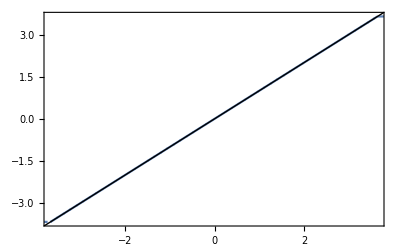

```mathematica
QuantilePlot[NormalDistribution[0,1]]
```

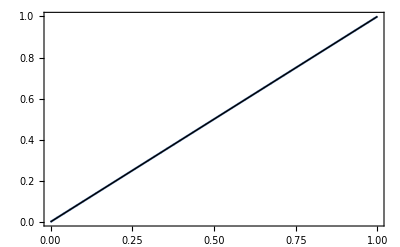

```mathematica
ProbabilityPlot[NormalDistribution[0,1]]
```

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
RandomVariate[NormalDistribution[0,1],100]
```

{0.85202,1.07189,1.87545,0.737534,0.105928,-0.86382,0.760364,1.16889,-0.989691,-0.823248,-0.186642,0.294986,0.479167,-1.66342,0.409201,0.029012,-1.08804,0.76116,0.096783,-1.23751,0.39831,0.804286,0.0994878,-0.630966,0.415499,-1.01575,-0.382942,-1.30368,0.407416,-0.288369,1.05161,-0.198225,0.785377,-1.27322,0.118206,0.970774,-0.569112,2.00724,-1.13416,-1.42312,2.70937,0.832817,-0.184771,0.488124,1.60941,-0.471012,0.760952,-2.04072,0.129268,-0.101527,1.22438,-1.50638,0.189643,0.894315,0.294294,-1.71408,0.215529,1.74042,0.705965,-0.936657,1.05623,-0.988855,0.489004,-2.42302,-0.646741,-0.317201,-2.63582,0.537383,-0.0889212,1.62141,0.00599786,-0.585203,-0.00263469,0.765716,0.705667,0.873825,1.96237,-0.24002,2.73797,-1.3728,-0.393695,-0.957821,1.00142,0.639774,0.948487,-0.1759,-1.37332,0.582227,-0.242239,-0.276402,0.839443,-0.966386,0.0132986,0.857076,0.364428,-0.202181,-0.440415,0.392987,1.31817,0.840788}

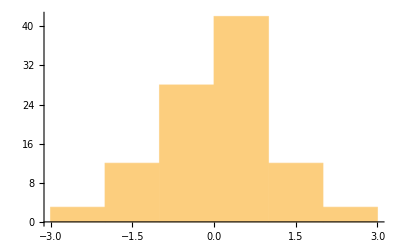

```mathematica
Histogram[%30]
```

```mathematica
Table[{i, RandomVariate[NormalDistribution[0,1]]}, {i, 1, 10}]
```

{{1,1.04534},{2,-1.60138},{3,-2.215},{4,2.5175},{5,1.21237},{6,1.19461},{7,-1.72157},{8,-0.837498},{9,-0.03318},{10,0.877138}}

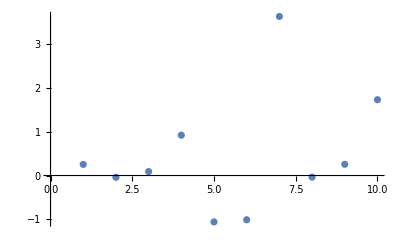

```mathematica
ListPlot[Table[{i, RandomVariate[NormalDistribution[0,1]]}, {i, 1, 10}]]
```

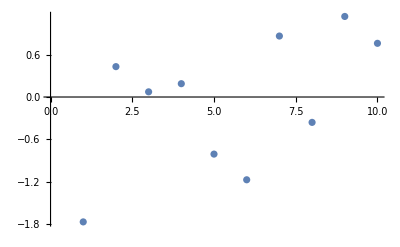

```mathematica
ListPlot[Table[{i, RandomVariate[NormalDistribution[0,1]]}, {i, 1, 10}]]
```

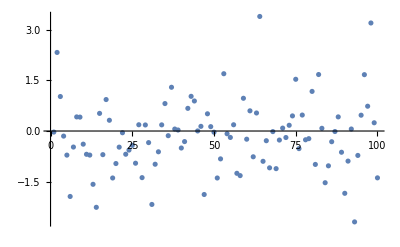

```mathematica
ListPlot[Table[{i, RandomVariate[NormalDistribution[0,1]]}, {i, 1, 100}]]
```

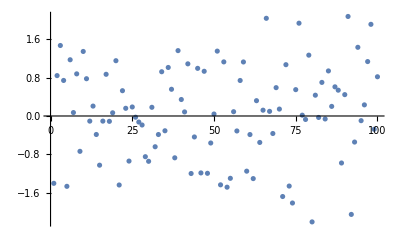

```mathematica
ListPlot[
Table[
{i, RandomVariate[NormalDistribution[0,1]]},
 {i, 1, 100}]]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

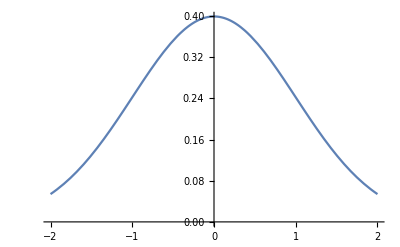

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-2,2}]
```

```mathematica
0==FullSimplify[
Normalize[D[{x, f[x]},x]].
Normalize[D[{x, x^2},x]], Element[x|f[x],Reals]]
```

0==(1+2 x f'[x])/(√((1+4 x^2) (1+Abs[f'[x]]^2)))

```mathematica
DSolve[0==(1+2 x f'[x])/(√((1+4 x^2) (1+Abs[f'[x]]^2))),{f[x]},{x}]
```

{{f[x]→C[1]-Log[x]/2}}

```mathematica
DSolve[
0==FullSimplify[
Normalize[D[{x, f[x]},x]].
Normalize[D[{x, x^3},x]], Element[x|f[x],Reals]], f[x], x]
```

{{f[x]→1/(3 x)+C[1]}}

```mathematica
Table[x^i,{i, 0, 50}]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50}

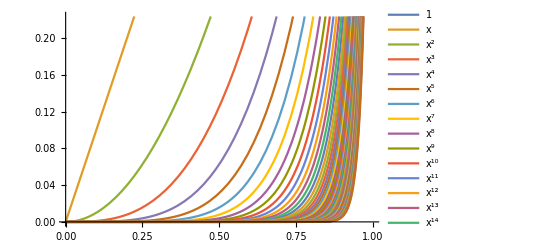

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50},
{x, 0, 1},  PlotLegends->"Expressions"]
```

```mathematica
0==FullSimplify[
Normalize[D[{x, f[x]},x]].
Normalize[D[{x, x^a},x]],Element[x|f[x]|a|f'[x], Reals]]
```

0==(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2)))

```mathematica
DSolve[0==(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2))),{f[x]},{x}]
```

{{f[x]→-x^(2-a)/((2-a) a)+C[1]}}

```mathematica
Table[
DSolve[0==(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2))),f[x],x], {a, 1,50, 1}]
```

{{{f[x]→-x+C[1]}},{{f[x]→C[1]-Log[x]/2}},{{f[x]→1/(3 x)+C[1]}},{{f[x]→1/(8 x^2)+C[1]}},{{f[x]→1/(15 x^3)+C[1]}},{{f[x]→1/(24 x^4)+C[1]}},{{f[x]→1/(35 x^5)+C[1]}},{{f[x]→1/(48 x^6)+C[1]}},{{f[x]→1/(63 x^7)+C[1]}},{{f[x]→1/(80 x^8)+C[1]}},{{f[x]→1/(99 x^9)+C[1]}},{{f[x]→1/(120 x^10)+C[1]}},{{f[x]→1/(143 x^11)+C[1]}},{{f[x]→1/(168 x^12)+C[1]}},{{f[x]→1/(195 x^13)+C[1]}},{{f[x]→1/(224 x^14)+C[1]}},{{f[x]→1/(255 x^15)+C[1]}},{{f[x]→1/(288 x^16)+C[1]}},{{f[x]→1/(323 x^17)+C[1]}},{{f[x]→1/(360 x^18)+C[1]}},{{f[x]→1/(399 x^19)+C[1]}},{{f[x]→1/(440 x^20)+C[1]}},{{f[x]→1/(483 x^21)+C[1]}},{{f[x]→1/(528 x^22)+C[1]}},{{f[x]→1/(575 x^23)+C[1]}},{{f[x]→1/(624 x^24)+C[1]}},{{f[x]→1/(675 x^25)+C[1]}},{{f[x]→1/(728 x^26)+C[1]}},{{f[x]→1/(783 x^27)+C[1]}},{{f[x]→1/(840 x^28)+C[1]}},{{f[x]→1/(899 x^29)+C[1]}},{{f[x]→1/(960 x^30)+C[1]}},{{f[x]→1/(1023 x^31)+C[1]}},{{f[x]→1/(1088 x^32)+C[1]}},{{f[x]→1/(1155 x^33)+C[1]}},{{f[x]→1/(1224 x^34)+C[1]}},{{f[x]→1/(1295 x^35)+C[1]}},{{f[x]→1/(1368 x^36)+C[1]}},{{f[x]→1/(1443 x^37)+C[1]}},{{f[x]→1/(1520 x^38)+C[1]}},{{f[x]→1/(1599 x^39)+C[1]}},{{f[x]→1/(1680 x^40)+C[1]}},{{f[x]→1/(1763 x^41)+C[1]}},{{f[x]→1/(1848 x^42)+C[1]}},{{f[x]→1/(1935 x^43)+C[1]}},{{f[x]→1/(2024 x^44)+C[1]}},{{f[x]→1/(2115 x^45)+C[1]}},{{f[x]→1/(2208 x^46)+C[1]}},{{f[x]→1/(2303 x^47)+C[1]}},{{f[x]→1/(2400 x^48)+C[1]}}}

```mathematica
f[x]/.%49
```

{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]},{1/(99 x^9)+C[1]},{1/(120 x^10)+C[1]},{1/(143 x^11)+C[1]},{1/(168 x^12)+C[1]},{1/(195 x^13)+C[1]},{1/(224 x^14)+C[1]},{1/(255 x^15)+C[1]},{1/(288 x^16)+C[1]},{1/(323 x^17)+C[1]},{1/(360 x^18)+C[1]},{1/(399 x^19)+C[1]},{1/(440 x^20)+C[1]},{1/(483 x^21)+C[1]},{1/(528 x^22)+C[1]},{1/(575 x^23)+C[1]},{1/(624 x^24)+C[1]},{1/(675 x^25)+C[1]},{1/(728 x^26)+C[1]},{1/(783 x^27)+C[1]},{1/(840 x^28)+C[1]},{1/(899 x^29)+C[1]},{1/(960 x^30)+C[1]},{1/(1023 x^31)+C[1]},{1/(1088 x^32)+C[1]},{1/(1155 x^33)+C[1]},{1/(1224 x^34)+C[1]},{1/(1295 x^35)+C[1]},{1/(1368 x^36)+C[1]},{1/(1443 x^37)+C[1]},{1/(1520 x^38)+C[1]},{1/(1599 x^39)+C[1]},{1/(1680 x^40)+C[1]},{1/(1763 x^41)+C[1]},{1/(1848 x^42)+C[1]},{1/(1935 x^43)+C[1]},{1/(2024 x^44)+C[1]},{1/(2115 x^45)+C[1]},{1/(2208 x^46)+C[1]},{1/(2303 x^47)+C[1]},{1/(2400 x^48)+C[1]}}

```mathematica
%49/.Rule->List
```

{{{{f[x],-x+C[1]}}},{{{f[x],C[1]-Log[x]/2}}},{{{f[x],1/(3 x)+C[1]}}},{{{f[x],1/(8 x^2)+C[1]}}},{{{f[x],1/(15 x^3)+C[1]}}},{{{f[x],1/(24 x^4)+C[1]}}},{{{f[x],1/(35 x^5)+C[1]}}},{{{f[x],1/(48 x^6)+C[1]}}},{{{f[x],1/(63 x^7)+C[1]}}},{{{f[x],1/(80 x^8)+C[1]}}},{{{f[x],1/(99 x^9)+C[1]}}},{{{f[x],1/(120 x^10)+C[1]}}},{{{f[x],1/(143 x^11)+C[1]}}},{{{f[x],1/(168 x^12)+C[1]}}},{{{f[x],1/(195 x^13)+C[1]}}},{{{f[x],1/(224 x^14)+C[1]}}},{{{f[x],1/(255 x^15)+C[1]}}},{{{f[x],1/(288 x^16)+C[1]}}},{{{f[x],1/(323 x^17)+C[1]}}},{{{f[x],1/(360 x^18)+C[1]}}},{{{f[x],1/(399 x^19)+C[1]}}},{{{f[x],1/(440 x^20)+C[1]}}},{{{f[x],1/(483 x^21)+C[1]}}},{{{f[x],1/(528 x^22)+C[1]}}},{{{f[x],1/(575 x^23)+C[1]}}},{{{f[x],1/(624 x^24)+C[1]}}},{{{f[x],1/(675 x^25)+C[1]}}},{{{f[x],1/(728 x^26)+C[1]}}},{{{f[x],1/(783 x^27)+C[1]}}},{{{f[x],1/(840 x^28)+C[1]}}},{{{f[x],1/(899 x^29)+C[1]}}},{{{f[x],1/(960 x^30)+C[1]}}},{{{f[x],1/(1023 x^31)+C[1]}}},{{{f[x],1/(1088 x^32)+C[1]}}},{{{f[x],1/(1155 x^33)+C[1]}}},{{{f[x],1/(1224 x^34)+C[1]}}},{{{f[x],1/(1295 x^35)+C[1]}}},{{{f[x],1/(1368 x^36)+C[1]}}},{{{f[x],1/(1443 x^37)+C[1]}}},{{{f[x],1/(1520 x^38)+C[1]}}},{{{f[x],1/(1599 x^39)+C[1]}}},{{{f[x],1/(1680 x^40)+C[1]}}},{{{f[x],1/(1763 x^41)+C[1]}}},{{{f[x],1/(1848 x^42)+C[1]}}},{{{f[x],1/(1935 x^43)+C[1]}}},{{{f[x],1/(2024 x^44)+C[1]}}},{{{f[x],1/(2115 x^45)+C[1]}}},{{{f[x],1/(2208 x^46)+C[1]}}},{{{f[x],1/(2303 x^47)+C[1]}}},{{{f[x],1/(2400 x^48)+C[1]}}}}

```mathematica
{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]},{1/(99 x^9)+C[1]},{1/(120 x^10)+C[1]},{1/(143 x^11)+C[1]},{1/(168 x^12)+C[1]},{1/(195 x^13)+C[1]},{1/(224 x^14)+C[1]},{1/(255 x^15)+C[1]},{1/(288 x^16)+C[1]},{1/(323 x^17)+C[1]},{1/(360 x^18)+C[1]},{1/(399 x^19)+C[1]},{1/(440 x^20)+C[1]},{1/(483 x^21)+C[1]},{1/(528 x^22)+C[1]},{1/(575 x^23)+C[1]},{1/(624 x^24)+C[1]},{1/(675 x^25)+C[1]},{1/(728 x^26)+C[1]},{1/(783 x^27)+C[1]},{1/(840 x^28)+C[1]},{1/(899 x^29)+C[1]},{1/(960 x^30)+C[1]},{1/(1023 x^31)+C[1]},{1/(1088 x^32)+C[1]},{1/(1155 x^33)+C[1]},{1/(1224 x^34)+C[1]},{1/(1295 x^35)+C[1]},{1/(1368 x^36)+C[1]},{1/(1443 x^37)+C[1]},{1/(1520 x^38)+C[1]},{1/(1599 x^39)+C[1]},{1/(1680 x^40)+C[1]},{1/(1763 x^41)+C[1]},{1/(1848 x^42)+C[1]},{1/(1935 x^43)+C[1]},{1/(2024 x^44)+C[1]},{1/(2115 x^45)+C[1]},{1/(2208 x^46)+C[1]},{1/(2303 x^47)+C[1]},{1/(2400 x^48)+C[1]}}/.C[1]->0
```

{{-x},{-Log[x]/2},{1/(3 x)},{1/(8 x^2)},{1/(15 x^3)},{1/(24 x^4)},{1/(35 x^5)},{1/(48 x^6)},{1/(63 x^7)},{1/(80 x^8)},{1/(99 x^9)},{1/(120 x^10)},{1/(143 x^11)},{1/(168 x^12)},{1/(195 x^13)},{1/(224 x^14)},{1/(255 x^15)},{1/(288 x^16)},{1/(323 x^17)},{1/(360 x^18)},{1/(399 x^19)},{1/(440 x^20)},{1/(483 x^21)},{1/(528 x^22)},{1/(575 x^23)},{1/(624 x^24)},{1/(675 x^25)},{1/(728 x^26)},{1/(783 x^27)},{1/(840 x^28)},{1/(899 x^29)},{1/(960 x^30)},{1/(1023 x^31)},{1/(1088 x^32)},{1/(1155 x^33)},{1/(1224 x^34)},{1/(1295 x^35)},{1/(1368 x^36)},{1/(1443 x^37)},{1/(1520 x^38)},{1/(1599 x^39)},{1/(1680 x^40)},{1/(1763 x^41)},{1/(1848 x^42)},{1/(1935 x^43)},{1/(2024 x^44)},{1/(2115 x^45)},{1/(2208 x^46)},{1/(2303 x^47)},{1/(2400 x^48)}}

```mathematica
Flatten[%52]
```

{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8),1/(99 x^9),1/(120 x^10),1/(143 x^11),1/(168 x^12),1/(195 x^13),1/(224 x^14),1/(255 x^15),1/(288 x^16),1/(323 x^17),1/(360 x^18),1/(399 x^19),1/(440 x^20),1/(483 x^21),1/(528 x^22),1/(575 x^23),1/(624 x^24),1/(675 x^25),1/(728 x^26),1/(783 x^27),1/(840 x^28),1/(899 x^29),1/(960 x^30),1/(1023 x^31),1/(1088 x^32),1/(1155 x^33),1/(1224 x^34),1/(1295 x^35),1/(1368 x^36),1/(1443 x^37),1/(1520 x^38),1/(1599 x^39),1/(1680 x^40),1/(1763 x^41),1/(1848 x^42),1/(1935 x^43),1/(2024 x^44),1/(2115 x^45),1/(2208 x^46),1/(2303 x^47),1/(2400 x^48)}

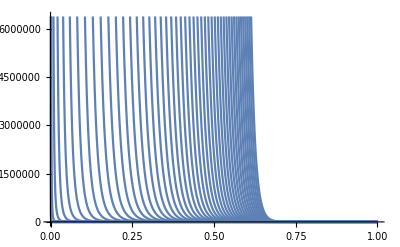

```mathematica
Plot[
Join[{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50},
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8),1/(99 x^9),1/(120 x^10),1/(143 x^11),1/(168 x^12),1/(195 x^13),1/(224 x^14),1/(255 x^15),1/(288 x^16),1/(323 x^17),1/(360 x^18),1/(399 x^19),1/(440 x^20),1/(483 x^21),1/(528 x^22),1/(575 x^23),1/(624 x^24),1/(675 x^25),1/(728 x^26),1/(783 x^27),1/(840 x^28),1/(899 x^29),1/(960 x^30),1/(1023 x^31),1/(1088 x^32),1/(1155 x^33),1/(1224 x^34),1/(1295 x^35),1/(1368 x^36),1/(1443 x^37),1/(1520 x^38),1/(1599 x^39),1/(1680 x^40),1/(1763 x^41),1/(1848 x^42),1/(1935 x^43),1/(2024 x^44),1/(2115 x^45),1/(2208 x^46),1/(2303 x^47),1/(2400 x^48)}],
{x, 0, 1},  PlotLegends->"Expressions"]
```

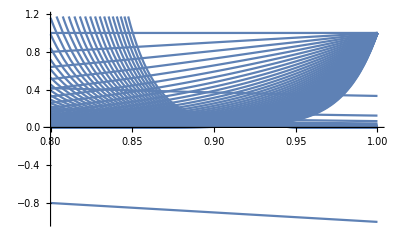

```mathematica
Plot[
Join[{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50},
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8),1/(99 x^9),1/(120 x^10),1/(143 x^11),1/(168 x^12),1/(195 x^13),1/(224 x^14),1/(255 x^15),1/(288 x^16),1/(323 x^17),1/(360 x^18),1/(399 x^19),1/(440 x^20),1/(483 x^21),1/(528 x^22),1/(575 x^23),1/(624 x^24),1/(675 x^25),1/(728 x^26),1/(783 x^27),1/(840 x^28),1/(899 x^29),1/(960 x^30),1/(1023 x^31),1/(1088 x^32),1/(1155 x^33),1/(1224 x^34),1/(1295 x^35),1/(1368 x^36),1/(1443 x^37),1/(1520 x^38),1/(1599 x^39),1/(1680 x^40),1/(1763 x^41),1/(1848 x^42),1/(1935 x^43),1/(2024 x^44),1/(2115 x^45),1/(2208 x^46),1/(2303 x^47),1/(2400 x^48)}],
{x, .8, 1},  PlotLegends->"Expressions"]
```

```mathematica
Table[
DSolve[0==(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2))),f[x],x], {a, 1,10, 1}]
```

{{{f[x]→-x+C[1]}},{{f[x]→C[1]-Log[x]/2}},{{f[x]→1/(3 x)+C[1]}},{{f[x]→1/(8 x^2)+C[1]}},{{f[x]→1/(15 x^3)+C[1]}},{{f[x]→1/(24 x^4)+C[1]}},{{f[x]→1/(35 x^5)+C[1]}},{{f[x]→1/(48 x^6)+C[1]}},{{f[x]→1/(63 x^7)+C[1]}},{{f[x]→1/(80 x^8)+C[1]}}}

```mathematica
f[x]/.%58
```

{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]}}

```mathematica
Flatten[{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]}}]
```

{-x+C[1],C[1]-Log[x]/2,1/(3 x)+C[1],1/(8 x^2)+C[1],1/(15 x^3)+C[1],1/(24 x^4)+C[1],1/(35 x^5)+C[1],1/(48 x^6)+C[1],1/(63 x^7)+C[1],1/(80 x^8)+C[1]}

```mathematica
{-x+C[1],C[1]-Log[x]/2,1/(3 x)+C[1],1/(8 x^2)+C[1],1/(15 x^3)+C[1],1/(24 x^4)+C[1],1/(35 x^5)+C[1],1/(48 x^6)+C[1],1/(63 x^7)+C[1],1/(80 x^8)+C[1]}/.C[1]->0
```

{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)}

```mathematica
Table[x^i,{i, 1, 10}]
```

{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

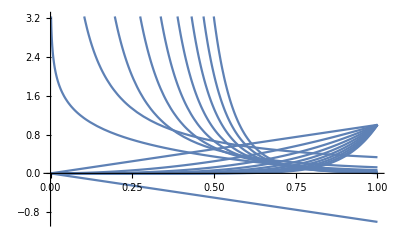

```mathematica
Plot[
Join[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)},
{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}
],{x, 0, 1}, PlotLegends->"Expressions"]
```

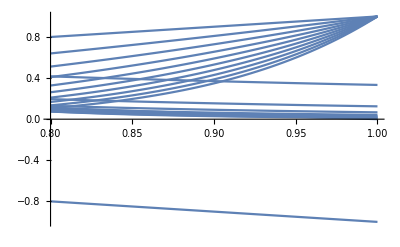

```mathematica
Plot[
Join[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)},
{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}
],{x, .8, 1}, PlotLegends->"Expressions"]
```

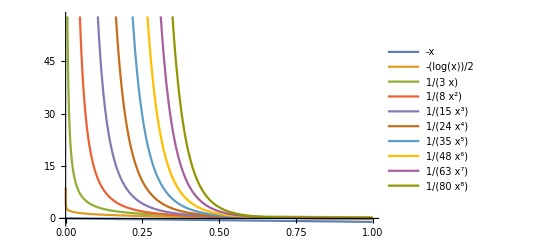

```mathematica
Plot[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)},
{x, 0, 1}, PlotLegends->"Expressions"]
```

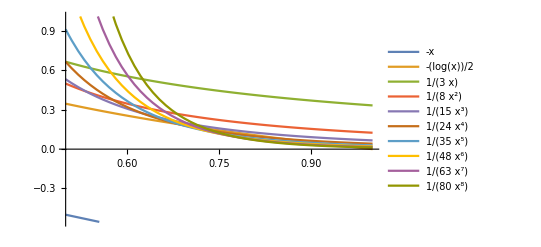

```mathematica
Plot[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)},
{x, 0.5, 1}, PlotLegends->"Expressions"]
```

```mathematica
WolframLanguageData[]
```

{$Aborted,$AllowExternalChannelFunctions,$AssertFunction,$Assumptions,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudBase,$CloudConnected,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudRootDirectory,$CloudSymbolBase,$CloudUserID,$CloudUserUUID,$CloudVersion,$CommandLine,$CompilationTarget,$ConfiguredKernels,$Context,$ContextPath,$ControlActiveSetting,$CookieStore,$Cookies,$CreationDate,$CurrentLink,$CurrentTask,$DateStringFormat,$DefaultAudioInputDevice,$DefaultAudioOutputDevice,$DefaultImagingDevice,$DefaultLocalBase,$DefaultNetworkInterface,$Display,$DisplayFunction,$DistributedContexts,$DynamicEvaluation,$Echo,$EmbedCodeEnvironments,$EmbeddableServices,$Epilog,$EvaluationCloudBase,$EvaluationCloudObject,$EvaluationEnvironment,$ExportFormats,$Failed,$FontFamilies,$FrontEnd,$FrontEndSession,$GeoLocation,$GeoLocationCity,$GeoLocationCountry,$GeoLocationSource,$HistoryLength,$HomeDirectory,$IgnoreEOF,$ImageFormattingWidth,$ImagingDevice,$ImagingDevices,$ImportFormats,$IncomingMailSettings,$InitialDirectory,$Initialization,$InitializationContexts,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDirectory,$InterpreterTypes,$IterationLimit,$KernelCount,$KernelID,$Language,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseServer,$Line,$Linked,$LocalBase,$LocalSymbolBase,$MachineAddresses,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinPrecision,$MobilePhone,$ModuleNumber,$NetworkConnected,$NetworkInterfaces,$NewMessage,$NewSymbol,$NoValue,$Notebooks,$NumberMarks,$OperatingSystem,$Output,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,4918,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeakStationarity,WeaklyConnectedComponents,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeatherData,WeatherForecastData,WebImageSearch,WebSearch,WeberE,Wedge,Wednesday,WeibullDistribution,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassHalfPeriods,WeierstrassInvariantG2,WeierstrassInvariantG3,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,WheelGraph,WhenEvent,Which,While,White,WhiteNoiseProcess,WhitePoint,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WikipediaData,WikipediaSearch,WilksW,WilksWTest,WindDirectionData,WindSpeedData,WindVectorData,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowMargins,WindowOpacity,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WinsorizedMean,WinsorizedVariance,WishartMatrixDistribution,With,WolframAlpha,WolframLanguageData,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,XYZColor,Xnor,Xor,Yellow,Yesterday,YuleDissimilarity,ZIPCodeData,ZTest,ZTransform,ZernikeR,ZeroSymmetric,ZeroTest,Zeta,ZetaZero,ZipfDistribution,ZoomCenter,ZoomFactor}
 |  |  |  |

```mathematica
Table[x^a,{a, 0, 50}]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50}

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50},{x, 0, 1}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FullSimplify[
Normalize[D[{x, f[x]},x]].
Normalize[D[{x, x^a},x]], And[Element[x|f[x]|f'[x],Reals], Element[a, Integers], 10≥a≥0]]
```

(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2)))

```mathematica
0==(x+a x^a f'[x])/(x √((1+(a x^(-1+a))^2) (1+f'[x]^2)))
```

```mathematica
FullSimplify[
Normalize[D[{x, f[x]},x]].
Normalize[D[{x, x^a},x]], And[Element[x|f[x]|f'[x]|a,Reals], 10≥a≥0]]
```

(x+a x^a f'[x])/(x √((1+Abs[a x^(-1+a)]^2) (1+f'[x]^2)))

```mathematica
0==(x+a x^a f'[x])/(x √((1+(a x^(-1+a))^2) (1+f'[x]^2)))
```

0==(x+a x^a f'[x])/(x √((1+a^2 x^(-2+2 a)) (1+f'[x]^2)))

```mathematica
DSolve[0==(x+a x^a f'[x])/(x √((1+a^2 x^(-2+2 a)) (1+f'[x]^2))),{f[x]},{x}]
```

{{f[x]→-x^(2-a)/((2-a) a)+C[1]}}

```mathematica
Table[
DSolve[0==(x+a x^a f'[x])/(x √((1+a^2 x^(-2+2 a)) (1+f'[x]^2))),f[x],x], {a, 1, 10,1}]
```

{{{f[x]→-x+C[1]}},{{f[x]→C[1]-Log[x]/2}},{{f[x]→1/(3 x)+C[1]}},{{f[x]→1/(8 x^2)+C[1]}},{{f[x]→1/(15 x^3)+C[1]}},{{f[x]→1/(24 x^4)+C[1]}},{{f[x]→1/(35 x^5)+C[1]}},{{f[x]→1/(48 x^6)+C[1]}},{{f[x]→1/(63 x^7)+C[1]}},{{f[x]→1/(80 x^8)+C[1]}}}

```mathematica
f[x]/.%75
```

{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]}}

```mathematica
Flatten[{{-x+C[1]},{C[1]-Log[x]/2},{1/(3 x)+C[1]},{1/(8 x^2)+C[1]},{1/(15 x^3)+C[1]},{1/(24 x^4)+C[1]},{1/(35 x^5)+C[1]},{1/(48 x^6)+C[1]},{1/(63 x^7)+C[1]},{1/(80 x^8)+C[1]}}]
```

{-x+C[1],C[1]-Log[x]/2,1/(3 x)+C[1],1/(8 x^2)+C[1],1/(15 x^3)+C[1],1/(24 x^4)+C[1],1/(35 x^5)+C[1],1/(48 x^6)+C[1],1/(63 x^7)+C[1],1/(80 x^8)+C[1]}

```mathematica
{-x+C[1],C[1]-Log[x]/2,1/(3 x)+C[1],1/(8 x^2)+C[1],1/(15 x^3)+C[1],1/(24 x^4)+C[1],1/(35 x^5)+C[1],1/(48 x^6)+C[1],1/(63 x^7)+C[1],1/(80 x^8)+C[1]}/.C[1]->0
```

{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)}

```mathematica
Manipulate[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)}, {x, 0,1}]
```

Power::indet: Indeterminate expression 0.^0. encountered.

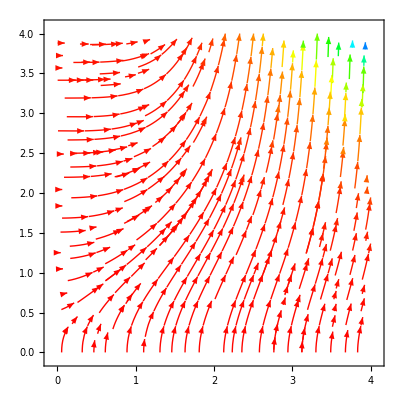

```mathematica
StreamPlot[{y,x^y}, {x, 0, 4}, {y,0,4}, StreamColorFunction->Hue]
```

```mathematica
Plot[
{-x,-Log[x]/2,1/(3 x),1/(8 x^2),1/(15 x^3),1/(24 x^4),1/(35 x^5),1/(48 x^6),1/(63 x^7),1/(80 x^8)},
{x, 0, 1}, PlotLegends->"Expressions"]
```

-Graphics-

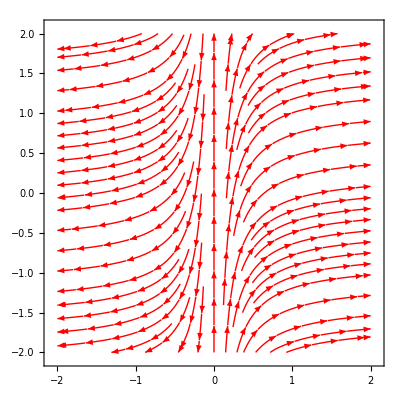

```mathematica
StreamPlot[
{x, 1/(3 x)}, {x, -2, 2}, {y,-2,2},StreamColorFunction->Hue]
```

```mathematica
{ 1/(3 x),-x}
```

{1/(3 x),-x}

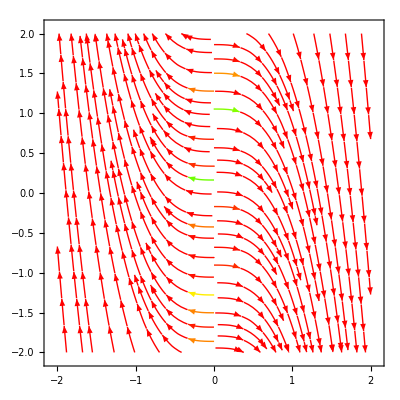

```mathematica
StreamPlot[
{1/(3 x),-x},
 {x, -2, 2}, {y,-2,2},
StreamColorFunction->Hue]
```

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

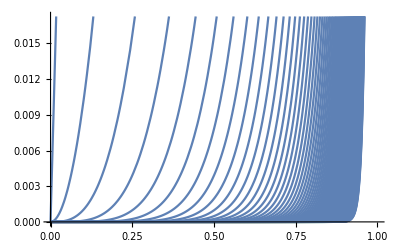

```mathematica
Plot[
Table[x^i,{i, 0, 100}],
{x, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
Plot[
Table[D[x^i,x],{i, 1, 3}],
{x, 0, 1}, PlotLegends->"Expressions"]
```

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Parallelize[Table[D[x^i,x],{i,0,100}]]
```

{0,1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9,11 x^10,12 x^11,13 x^12,14 x^13,15 x^14,16 x^15,17 x^16,18 x^17,19 x^18,20 x^19,21 x^20,22 x^21,23 x^22,24 x^23,25 x^24,26 x^25,27 x^26,28 x^27,29 x^28,30 x^29,31 x^30,32 x^31,33 x^32,34 x^33,35 x^34,36 x^35,37 x^36,38 x^37,39 x^38,40 x^39,41 x^40,42 x^41,43 x^42,44 x^43,45 x^44,46 x^45,47 x^46,48 x^47,49 x^48,50 x^49,51 x^50,52 x^51,53 x^52,54 x^53,55 x^54,56 x^55,57 x^56,58 x^57,59 x^58,60 x^59,61 x^60,62 x^61,63 x^62,64 x^63,65 x^64,66 x^65,67 x^66,68 x^67,69 x^68,70 x^69,71 x^70,72 x^71,73 x^72,74 x^73,75 x^74,76 x^75,77 x^76,78 x^77,79 x^78,80 x^79,81 x^80,82 x^81,83 x^82,84 x^83,85 x^84,86 x^85,87 x^86,88 x^87,89 x^88,90 x^89,91 x^90,92 x^91,93 x^92,94 x^93,95 x^94,96 x^95,97 x^96,98 x^97,99 x^98,100 x^99}

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

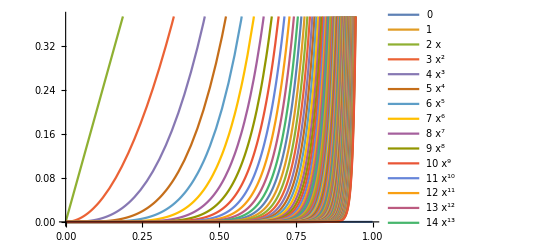

```mathematica
Plot[
{0,1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9,11 x^10,12 x^11,13 x^12,14 x^13,15 x^14,16 x^15,17 x^16,18 x^17,19 x^18,20 x^19,21 x^20,22 x^21,23 x^22,24 x^23,25 x^24,26 x^25,27 x^26,28 x^27,29 x^28,30 x^29,31 x^30,32 x^31,33 x^32,34 x^33,35 x^34,36 x^35,37 x^36,38 x^37,39 x^38,40 x^39,41 x^40,42 x^41,43 x^42,44 x^43,45 x^44,46 x^45,47 x^46,48 x^47,49 x^48,50 x^49,51 x^50,52 x^51,53 x^52,54 x^53,55 x^54,56 x^55,57 x^56,58 x^57,59 x^58,60 x^59,61 x^60,62 x^61,63 x^62,64 x^63,65 x^64,66 x^65,67 x^66,68 x^67,69 x^68,70 x^69,71 x^70,72 x^71,73 x^72,74 x^73,75 x^74,76 x^75,77 x^76,78 x^77,79 x^78,80 x^79,81 x^80,82 x^81,83 x^82,84 x^83,85 x^84,86 x^85,87 x^86,88 x^87,89 x^88,90 x^89,91 x^90,92 x^91,93 x^92,94 x^93,95 x^94,96 x^95,97 x^96,98 x^97,99 x^98,100 x^99},
{x,0,1},PlotLegends->"Expressions"]
```

```mathematica
Parallelize[Table[D[x^i,x],{i,0,1000}]]
```

{0,1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9,11 x^10,12 x^11,13 x^12,14 x^13,15 x^14,16 x^15,17 x^16,18 x^17,19 x^18,20 x^19,21 x^20,22 x^21,23 x^22,24 x^23,25 x^24,26 x^25,27 x^26,28 x^27,29 x^28,30 x^29,31 x^30,32 x^31,33 x^32,34 x^33,35 x^34,36 x^35,37 x^36,38 x^37,39 x^38,40 x^39,41 x^40,42 x^41,43 x^42,44 x^43,45 x^44,46 x^45,47 x^46,48 x^47,49 x^48,50 x^49,51 x^50,52 x^51,53 x^52,54 x^53,55 x^54,56 x^55,57 x^56,58 x^57,59 x^58,60 x^59,61 x^60,62 x^61,63 x^62,64 x^63,65 x^64,66 x^65,67 x^66,68 x^67,69 x^68,70 x^69,71 x^70,72 x^71,73 x^72,74 x^73,75 x^74,76 x^75,77 x^76,78 x^77,79 x^78,80 x^79,81 x^80,82 x^81,83 x^82,84 x^83,85 x^84,86 x^85,87 x^86,88 x^87,89 x^88,90 x^89,91 x^90,92 x^91,93 x^92,94 x^93,95 x^94,96 x^95,97 x^96,98 x^97,99 x^98,100 x^99,101 x^100,102 x^101,103 x^102,104 x^103,105 x^104,106 x^105,107 x^106,108 x^107,109 x^108,110 x^109,111 x^110,112 x^111,113 x^112,114 x^113,115 x^114,116 x^115,117 x^116,118 x^117,119 x^118,120 x^119,121 x^120,122 x^121,123 x^122,124 x^123,125 x^124,126 x^125,127 x^126,128 x^127,129 x^128,130 x^129,131 x^130,132 x^131,133 x^132,134 x^133,135 x^134,136 x^135,137 x^136,138 x^137,139 x^138,140 x^139,141 x^140,142 x^141,143 x^142,144 x^143,145 x^144,146 x^145,147 x^146,148 x^147,149 x^148,150 x^149,151 x^150,152 x^151,153 x^152,154 x^153,155 x^154,156 x^155,157 x^156,158 x^157,159 x^158,160 x^159,161 x^160,162 x^161,163 x^162,164 x^163,165 x^164,166 x^165,167 x^166,168 x^167,169 x^168,170 x^169,171 x^170,172 x^171,173 x^172,174 x^173,175 x^174,176 x^175,177 x^176,178 x^177,179 x^178,180 x^179,181 x^180,182 x^181,183 x^182,184 x^183,185 x^184,186 x^185,187 x^186,188 x^187,189 x^188,190 x^189,191 x^190,192 x^191,193 x^192,194 x^193,195 x^194,196 x^195,197 x^196,198 x^197,199 x^198,200 x^199,201 x^200,202 x^201,203 x^202,204 x^203,205 x^204,206 x^205,207 x^206,208 x^207,209 x^208,210 x^209,211 x^210,212 x^211,213 x^212,214 x^213,215 x^214,216 x^215,217 x^216,218 x^217,219 x^218,220 x^219,221 x^220,222 x^221,223 x^222,224 x^223,225 x^224,226 x^225,227 x^226,228 x^227,229 x^228,230 x^229,231 x^230,232 x^231,233 x^232,234 x^233,235 x^234,236 x^235,237 x^236,238 x^237,239 x^238,240 x^239,241 x^240,242 x^241,243 x^242,244 x^243,245 x^244,246 x^245,247 x^246,248 x^247,249 x^248,250 x^249,251 x^250,252 x^251,253 x^252,254 x^253,255 x^254,256 x^255,257 x^256,258 x^257,259 x^258,260 x^259,261 x^260,262 x^261,263 x^262,264 x^263,265 x^264,266 x^265,267 x^266,268 x^267,269 x^268,270 x^269,271 x^270,272 x^271,273 x^272,274 x^273,275 x^274,276 x^275,277 x^276,278 x^277,279 x^278,280 x^279,281 x^280,282 x^281,283 x^282,284 x^283,285 x^284,286 x^285,287 x^286,288 x^287,289 x^288,290 x^289,291 x^290,292 x^291,293 x^292,294 x^293,295 x^294,296 x^295,297 x^296,298 x^297,299 x^298,300 x^299,301 x^300,302 x^301,303 x^302,304 x^303,305 x^304,306 x^305,307 x^306,308 x^307,309 x^308,310 x^309,311 x^310,312 x^311,313 x^312,314 x^313,315 x^314,316 x^315,317 x^316,318 x^317,319 x^318,320 x^319,321 x^320,322 x^321,323 x^322,324 x^323,325 x^324,326 x^325,327 x^326,328 x^327,329 x^328,330 x^329,331 x^330,332 x^331,333 x^332,334 x^333,335 x^334,336 x^335,337 x^336,338 x^337,339 x^338,340 x^339,341 x^340,342 x^341,343 x^342,344 x^343,345 x^344,346 x^345,347 x^346,348 x^347,349 x^348,350 x^349,351 x^350,352 x^351,353 x^352,354 x^353,355 x^354,356 x^355,357 x^356,358 x^357,359 x^358,360 x^359,361 x^360,362 x^361,363 x^362,364 x^363,365 x^364,366 x^365,367 x^366,368 x^367,369 x^368,370 x^369,371 x^370,372 x^371,373 x^372,374 x^373,375 x^374,376 x^375,377 x^376,378 x^377,379 x^378,380 x^379,381 x^380,382 x^381,383 x^382,384 x^383,385 x^384,386 x^385,387 x^386,388 x^387,389 x^388,390 x^389,391 x^390,392 x^391,393 x^392,394 x^393,395 x^394,396 x^395,397 x^396,398 x^397,399 x^398,400 x^399,401 x^400,402 x^401,403 x^402,404 x^403,405 x^404,406 x^405,407 x^406,408 x^407,409 x^408,410 x^409,411 x^410,412 x^411,413 x^412,414 x^413,415 x^414,416 x^415,417 x^416,418 x^417,419 x^418,420 x^419,421 x^420,422 x^421,423 x^422,424 x^423,425 x^424,426 x^425,427 x^426,428 x^427,429 x^428,430 x^429,431 x^430,432 x^431,433 x^432,434 x^433,435 x^434,436 x^435,437 x^436,438 x^437,439 x^438,440 x^439,441 x^440,442 x^441,443 x^442,444 x^443,445 x^444,446 x^445,447 x^446,448 x^447,449 x^448,450 x^449,451 x^450,452 x^451,453 x^452,454 x^453,455 x^454,456 x^455,457 x^456,458 x^457,459 x^458,460 x^459,461 x^460,462 x^461,463 x^462,464 x^463,465 x^464,466 x^465,467 x^466,468 x^467,469 x^468,470 x^469,471 x^470,472 x^471,473 x^472,474 x^473,475 x^474,476 x^475,477 x^476,478 x^477,479 x^478,480 x^479,481 x^480,482 x^481,483 x^482,484 x^483,485 x^484,486 x^485,487 x^486,488 x^487,489 x^488,490 x^489,491 x^490,492 x^491,493 x^492,494 x^493,495 x^494,496 x^495,497 x^496,498 x^497,499 x^498,500 x^499,501 x^500,502 x^501,503 x^502,504 x^503,505 x^504,506 x^505,507 x^506,508 x^507,509 x^508,510 x^509,511 x^510,512 x^511,513 x^512,514 x^513,515 x^514,516 x^515,517 x^516,518 x^517,519 x^518,520 x^519,521 x^520,522 x^521,523 x^522,524 x^523,525 x^524,526 x^525,527 x^526,528 x^527,529 x^528,530 x^529,531 x^530,532 x^531,533 x^532,534 x^533,535 x^534,536 x^535,537 x^536,538 x^537,539 x^538,540 x^539,541 x^540,542 x^541,543 x^542,544 x^543,545 x^544,546 x^545,547 x^546,548 x^547,549 x^548,550 x^549,551 x^550,552 x^551,553 x^552,554 x^553,555 x^554,556 x^555,557 x^556,558 x^557,559 x^558,560 x^559,561 x^560,562 x^561,563 x^562,564 x^563,565 x^564,566 x^565,567 x^566,568 x^567,569 x^568,570 x^569,571 x^570,572 x^571,573 x^572,574 x^573,575 x^574,576 x^575,577 x^576,578 x^577,579 x^578,580 x^579,581 x^580,582 x^581,583 x^582,584 x^583,585 x^584,586 x^585,587 x^586,588 x^587,589 x^588,590 x^589,591 x^590,592 x^591,593 x^592,594 x^593,595 x^594,596 x^595,597 x^596,598 x^597,599 x^598,600 x^599,601 x^600,602 x^601,603 x^602,604 x^603,605 x^604,606 x^605,607 x^606,608 x^607,609 x^608,610 x^609,611 x^610,612 x^611,613 x^612,614 x^613,615 x^614,616 x^615,617 x^616,618 x^617,619 x^618,620 x^619,621 x^620,622 x^621,623 x^622,624 x^623,625 x^624,626 x^625,627 x^626,628 x^627,629 x^628,630 x^629,631 x^630,632 x^631,633 x^632,634 x^633,635 x^634,636 x^635,637 x^636,638 x^637,639 x^638,640 x^639,641 x^640,642 x^641,643 x^642,644 x^643,645 x^644,646 x^645,647 x^646,648 x^647,649 x^648,650 x^649,651 x^650,652 x^651,653 x^652,654 x^653,655 x^654,656 x^655,657 x^656,658 x^657,659 x^658,660 x^659,661 x^660,662 x^661,663 x^662,664 x^663,665 x^664,666 x^665,667 x^666,668 x^667,669 x^668,670 x^669,671 x^670,672 x^671,673 x^672,674 x^673,675 x^674,676 x^675,677 x^676,678 x^677,679 x^678,680 x^679,681 x^680,682 x^681,683 x^682,684 x^683,685 x^684,686 x^685,687 x^686,688 x^687,689 x^688,690 x^689,691 x^690,692 x^691,693 x^692,694 x^693,695 x^694,696 x^695,697 x^696,698 x^697,699 x^698,700 x^699,701 x^700,702 x^701,703 x^702,704 x^703,705 x^704,706 x^705,707 x^706,708 x^707,709 x^708,710 x^709,711 x^710,712 x^711,713 x^712,714 x^713,715 x^714,716 x^715,717 x^716,718 x^717,719 x^718,720 x^719,721 x^720,722 x^721,723 x^722,724 x^723,725 x^724,726 x^725,727 x^726,728 x^727,729 x^728,730 x^729,731 x^730,732 x^731,733 x^732,734 x^733,735 x^734,736 x^735,737 x^736,738 x^737,739 x^738,740 x^739,741 x^740,742 x^741,743 x^742,744 x^743,745 x^744,746 x^745,747 x^746,748 x^747,749 x^748,750 x^749,751 x^750,752 x^751,753 x^752,754 x^753,755 x^754,756 x^755,757 x^756,758 x^757,759 x^758,760 x^759,761 x^760,762 x^761,763 x^762,764 x^763,765 x^764,766 x^765,767 x^766,768 x^767,769 x^768,770 x^769,771 x^770,772 x^771,773 x^772,774 x^773,775 x^774,776 x^775,777 x^776,778 x^777,779 x^778,780 x^779,781 x^780,782 x^781,783 x^782,784 x^783,785 x^784,786 x^785,787 x^786,788 x^787,789 x^788,790 x^789,791 x^790,792 x^791,793 x^792,794 x^793,795 x^794,796 x^795,797 x^796,798 x^797,799 x^798,800 x^799,801 x^800,802 x^801,803 x^802,804 x^803,805 x^804,806 x^805,807 x^806,808 x^807,809 x^808,810 x^809,811 x^810,812 x^811,813 x^812,814 x^813,815 x^814,816 x^815,817 x^816,818 x^817,819 x^818,820 x^819,821 x^820,822 x^821,823 x^822,824 x^823,825 x^824,826 x^825,827 x^826,828 x^827,829 x^828,830 x^829,831 x^830,832 x^831,833 x^832,834 x^833,835 x^834,836 x^835,837 x^836,838 x^837,839 x^838,840 x^839,841 x^840,842 x^841,843 x^842,844 x^843,845 x^844,846 x^845,847 x^846,848 x^847,849 x^848,850 x^849,851 x^850,852 x^851,853 x^852,854 x^853,855 x^854,856 x^855,857 x^856,858 x^857,859 x^858,860 x^859,861 x^860,862 x^861,863 x^862,864 x^863,865 x^864,866 x^865,867 x^866,868 x^867,869 x^868,870 x^869,871 x^870,872 x^871,873 x^872,874 x^873,875 x^874,876 x^875,877 x^876,878 x^877,879 x^878,880 x^879,881 x^880,882 x^881,883 x^882,884 x^883,885 x^884,886 x^885,887 x^886,888 x^887,889 x^888,890 x^889,891 x^890,892 x^891,893 x^892,894 x^893,895 x^894,896 x^895,897 x^896,898 x^897,899 x^898,900 x^899,901 x^900,902 x^901,903 x^902,904 x^903,905 x^904,906 x^905,907 x^906,908 x^907,909 x^908,910 x^909,911 x^910,912 x^911,913 x^912,914 x^913,915 x^914,916 x^915,917 x^916,918 x^917,919 x^918,920 x^919,921 x^920,922 x^921,923 x^922,924 x^923,925 x^924,926 x^925,927 x^926,928 x^927,929 x^928,930 x^929,931 x^930,932 x^931,933 x^932,934 x^933,935 x^934,936 x^935,937 x^936,938 x^937,939 x^938,940 x^939,941 x^940,942 x^941,943 x^942,944 x^943,945 x^944,946 x^945,947 x^946,948 x^947,949 x^948,950 x^949,951 x^950,952 x^951,953 x^952,954 x^953,955 x^954,956 x^955,957 x^956,958 x^957,959 x^958,960 x^959,961 x^960,962 x^961,963 x^962,964 x^963,965 x^964,966 x^965,967 x^966,968 x^967,969 x^968,970 x^969,971 x^970,972 x^971,973 x^972,974 x^973,975 x^974,976 x^975,977 x^976,978 x^977,979 x^978,980 x^979,981 x^980,982 x^981,983 x^982,984 x^983,985 x^984,986 x^985,987 x^986,988 x^987,989 x^988,990 x^989,991 x^990,992 x^991,993 x^992,994 x^993,995 x^994,996 x^995,997 x^996,998 x^997,999 x^998,1000 x^999}

```mathematica
Plot[
Out[95],
{x,0,1},PlotLegends->"Expressions"]
```

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Manipulate[
Plot[x^a,{x,0,1}, PlotLegends->"Expressions"],
{a, 0, 50}]
```

```mathematica
Times[a,b]
```

a b

```mathematica
Plot3D[a b,{a,-1.,1.},{b,-1.,1.}]
```

-Graphics3D-

```mathematica
Plus[a,b,Plus[c]]
```

a+b+c

```mathematica
A↦B
```

Function[A,B]

```mathematica
Function[A,B][4]
```

B

```mathematica
Function[A,B]'
```

Function[A,0]

```mathematica
x↦x
```

Function[x,x]

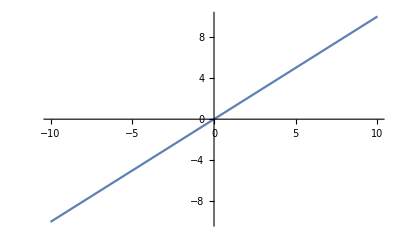

```mathematica
Plot[Function[x,x][x],{x,-10,10}]
```

```mathematica
x↦x^2
```

Function[x,x^2]

```mathematica
Function[x,x^2][3]
```

9

```mathematica
x↦x[x↦x]
```

Function[x,x[Function[x,x]]]

```mathematica
Plot[Function[x,x[Function[x,x]]][x],{x,-8,8}]
```

-Graphics-

```mathematica
(x↦x)[x↦x]
```

Function[x,x]

```mathematica
x↦x[x]
```

Function[x,x[x]]

```mathematica
Plot[Function[x,x[x]][x],{x,-8,8}]
```

-Graphics-

```mathematica
x↦x[x][Identity]
```

Function[x,x[x][Identity]]

```mathematica
Attributes[let] = {HoldFirst};
```

```mathematica
(λ[x_]·expr2_)[expr1_] :=let[{x=expr1}, expr2]
```

```mathematica
let[{x_=expr_}, x_] := expr;
let[{x_=expr_},y_] /;!StringQ[y]&&!NumberQ[y]:= y /;x=!=y;
let[{x_=expr1_}, expr2_[expr3_]] :=
	       let[{x=expr1}, expr2][let[{x=expr1}, expr3]];
let[{x_=expr1_}, (λ[x_]·expr2_)]:=(λ[x]·expr2);
let[{x_=expr1_}, (λ[y_]·expr2_)]:=
	     (λ[y]·let[{x=expr1}, expr2])/;
		   (x=!=y)&&Not[MemberQ[freeVars[expr1], y]];
let[{x_=expr1_}, (λ[y_]·expr2_)]:=
	     let[{x=expr1}, ((λ[y]·expr2)/.y->Unique["q"])]/;
		   (x=!=y)&&MemberQ[freeVars[expr1], y];
```

```mathematica
freeVars[x_] := {x};
freeVars[expr1_[expr2_]] :=
	      Union[freeVars[expr1], freeVars[expr2]];
freeVars[(λ[x_]·expr_)]:=Select[freeVars[expr], (#=!=x&)]
```

```mathematica
true=(λ[x]·(λ[y]·x));
false=(λ[x]·(λ[y]·y));
if=(λ[p]·(λ[x]·(λ[y]·p[x][y])));
```

```mathematica
churchN[n_] :=λ[f]·(λ[x]·Nest[f[#]&, x, n])
```

```mathematica
succ=λ[n]·(λ[f]·(λ[x]·(n[f])[f[x]]));
iszero=λ[n]·(n[(λ[x]·false)])[true];
add=λ[m]·(λ[n]·(λ[f]·(λ[x]·(m[f])[n[f][x]])));
mult=λ[m]·(λ[n]·(λ[f]·m[n[f]]));
exp=λ[m]·(λ[n]·(λ[f]·(λ[x]·((n[m])[f])[x])));
```

```mathematica
Manipulate[With[{op=Which[operation=="successor",succ,operation=="is zero?",iszero,operation=="addition",add,operation=="multiplication",mult,operation=="exponentiation",exp]},Pane[Text@Style[If[MemberQ[{"successor","is zero?"},operation],HoldForm[op][n1]==op[churchN[n1]],HoldForm[op][n1][n2]==op[churchN[n1]][churchN[n2]]],18,LineIndent->0],{600,250},Alignment->{Center,Center}]],{{n1,0,"first numeral"},0,5,1,ControlType->Setter},{{n2,3,"second numeral"},0,3,1,ControlType->Setter,Enabled->Dynamic[MemberQ[{"addition","multiplication","exponentiation"},operation]]},{{operation,"addition"},{"successor","is zero?","addition","multiplication","exponentiation"}},SaveDefinitions->True]
```

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
Identity[Plus[a,b]]==Plus[Identity[a],Identity[b]]
```

True